```mathematica
Hz=100*h*Sqrt[e];
e=Ωm(1+z)^3+Ωr(1+z)^4+Ωk(1+z)^2+Ωϕ*(1+z)^(3+3w0+3wa)*E^(-3wa*z/(1+z));
```

```mathematica
DE = 3Ωm(1+z)^2+4Ωr(1+z)^3+2Ωk(1+z)+opp;
opp=3(1+w0+z+w0*z+wa*z)*(1+z)^(1+3w0+3wa)*Ωϕ*E^(-3wa*z/(1+z));
```

```mathematica
H0=100h
```

100 h

```mathematica
gpp=((1+z)*Hz)^2;
gp=(1+z)*Hz^2-(1+z)^2*DE*H0^2/2
g=3/2*Ωm*H0^2*(1+z)^3
```

10000 h^2 (1+z) ((1+z)^2 Ωk+(1+z)^3 Ωm+(1+z)^4 Ωr+ⅇ^(-(3 wa z)/(1+z)) (1+z)^(3+3 w0+3 wa) Ωϕ)-1/2 H0^2 (1+z)^2 (2 (1+z) Ωk+3 (1+z)^2 Ωm+4 (1+z)^3 Ωr+3 ⅇ^(-(3 wa z)/(1+z)) (1+z)^(1+3 w0+3 wa) (1+w0+z+w0 z+wa z) Ωϕ)

3/2 H0^2 (1+z)^3 Ωm

```mathematica
growth1=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]]
growth9=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.675,Ωm->0.246+0.050,Ωϕ->0.704,w0->-0.9,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth11=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.746,Ωm->0.201+0.041,Ωϕ->0.758,w0->-1.1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growthpos=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.776,Ωm->0.186+0.038,Ωϕ->0.766,w0->-1,wa->0,Ωr->0,Ωk->0.01},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growthneg=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.661,Ωm->0.256+0.052,Ωϕ->0.702,w0->-1,wa->0,Ωr->0,Ωk->-0.01},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth5=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0.5,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth15=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->-0.5,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
```

InterpolatingFunction[{{0., 9.}}, <>]

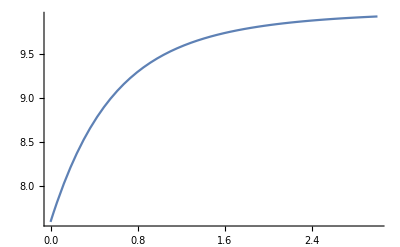

```mathematica
Plot[(1+z)growth1[z],{z,0,3},PlotRange->All]
```

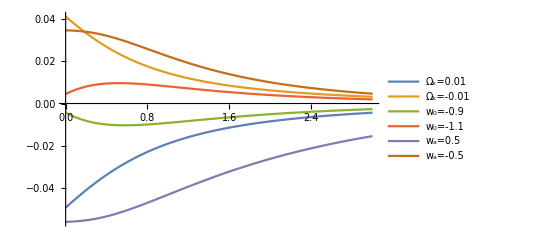

```mathematica
Plot[{(growthpos[z]-growth1[z])/growth1[z],(growthneg[z]-growth1[z])/growth1[z],(growth9[z]-growth1[z])/growth1[z],(growth11[z]-growth1[z])/growth1[z],(growth5[z]-growth1[z])/growth1[z],(growth15[z]-growth1[z])/growth1[z]},{z,0,3},PlotRange->All, PlotLegends->{"Ω_k=0.01","Ω_k=-0.01","w_0=-0.9","w_0=-1.1","w_a=0.5","w_a=-0.5"}]
```

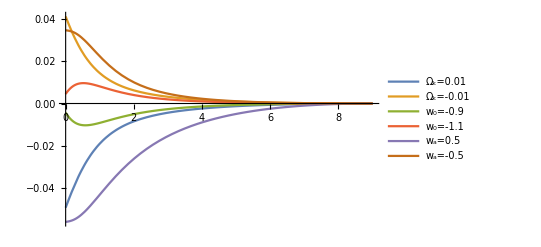

```mathematica
Plot[{(growthpos[z]-growth1[z])/growth1[z],(growthneg[z]-growth1[z])/growth1[z],(growth9[z]-growth1[z])/growth1[z],(growth11[z]-growth1[z])/growth1[z],(growth5[z]-growth1[z])/growth1[z],(growth15[z]-growth1[z])/growth1[z]},{z,0,9},PlotRange->All, PlotLegends->{"Ω_k=0.01","Ω_k=-0.01","w_0=-0.9","w_0=-1.1","w_a=0.5","w_a=-0.5"}]
```